### Street generation algorithm

Our generateRoads[] function uses recursive subdivision to create roads and Perlin Noise to introduce randomness to the density of roads in an area.

#### Code Breakdown

For our street generation, we will use a couple different helper functions:

A smoothing function to interpolate between a low and high bound based on x:

Our function will take in the dimensions of the city(worldWidth, worldHeight), the minimum size of a city block(minBlock), the maximum amount of random displacement applied to road splits(maxJitter), the width of the roads being generated(roadWidth), and frequency for the Perlin noise function(noiseFreq), lower and upper bound for interpolation(lowCutoff, highCutoff).

We will also initialize a stack(list that will contain the roads we will split) and roads(an empty list that will store generate roads)

Start of the generateRoads function taking in parameters and initializing stack and roads:

generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=
Module[{stack,roads={}}]

generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=
Module[{stack,roads={},addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor}]

#### Final Code

```mathematica
smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  jitter[max_]:=RandomReal[{-max,max}];
 clamp[val_,min_,max_]:=Min[Max[val,min],max];
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
```

```mathematica
(*recursiveRoadAdd[]*)
```

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack={{0,0,worldWidth,worldHeight}},roads={},addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False},
    
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit, sizeFactor},
    R=First[stack];
    stack=Rest[stack];
    
    n=octavePerlin[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2,0,4,0.5];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

## Steps for city generation

1. Start with a random base using a noise randomizer
	a. need to decide structure
	b. possible choices: tiling with each tile representing a different thing, polygons(nodes from that one article) 
2. From the base, generate more of the city
	a. Again we can use the nodes article where we can classify areas
	b. We can use wave function collapse: https://community.wolfram.com/groups/-/m/t/2435403
		wave function collapse is supposed to be easily compatible due to allowing support constraints so try my best to do that
* if we have extra time, add an option to be able to manually choose which base structure we start with.

possible tiles:
- street
- road
- building

### Perlin noise function(generating base city)

```mathematica
permutation = RandomSample[Range[1, 255]];
p = Join[permutation, permutation]; (*repeat it to avoid overflow*)
repeat = 255;
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);
```

```mathematica
perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 254], yi = Min[Floor[b], 254], zi = Min[Floor[c], 254], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
Rescale[lerp[y1, y2, w], {-1.2, 1.2}]];
```

```mathematica
octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

```mathematica
octaves=RandomInteger[{2, 3}];persistence=RandomReal[{0.2,0.4}];
ex = Table[octavePerlin[RandomInteger[{0, 10}], RandomInteger[{0, 10}], RandomReal[{0, 10}], octaves, persistence], 10];
Max[ex]
Min[ex]
Mean[ex]
```

```mathematica
perlin[1,2,0.010]
```

0.495837

```mathematica
Plot3D[octavePerlin[x,y,250,6,0.8],{x,20,21},{y,10,11}]
```

-Graphics3D-

```mathematica
Plot3D[octavePerlin[x,y,0.06,6,0.6],{x,22,21},{y,10,11}]
```

-Graphics3D-

### Road generation(binary recursion+perlin noise)

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor},
    
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  stack={{0,0,worldWidth,worldHeight}};

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
(*sizeFactor=Echo[smoothstep[1,2,Min[R[[3]]/minBlock,R[[4]]/minBlock]]];*)
(*sizeFactor=1;*)
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

## Map Generation(appl of funcs)

```mathematica
worldWidth=250;
worldHeight=250;
minBlock=15;
maxJitter=5;
roadWidth=5;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
```

### Entity filling (parks, building, etc .) w/noisemap

0.551531

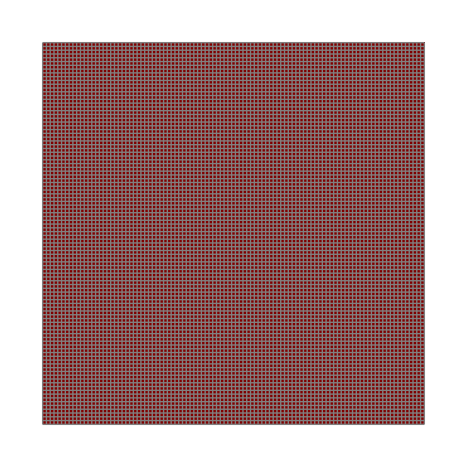

```mathematica
z=RandomReal[{0,255}];
octaves=6;
persistence=RandomReal[{0.5, 0.6}]
xcoef=RandomInteger[{0, 100}];ycoef=RandomInteger[{0,100}];
offset={0.37, 0.57};
(*noiseMap=Table[Mean[Flatten[Table[octavePerlin[a, b,z,octaves,persistence ], {a, x, x+10},{b, y, y+10}]]], {x, 1,100, 10},{y,1,100, 10}]*)
noiseMap=Table[octavePerlin[x+offset[[1]],y+0offset[[2]],z,octaves,persistence ],{x,xcoef,xcoef+5,0.05},{y,ycoef,ycoef+5,0.05}];
(*NEED TO FIGURE HOW TO MAKE THE NOISE THINGY ACC OKISH*)
classifyEntityTile[val_]:=Which[val<0.485,"park", val<0.52,"building", True, "background"];

tileColors=<|"road"->Black,"background"->White,"park" -> Green, "building"->Blue|>;
tileToNumber=AssociationThread[Keys[tileColors],Range[Length[tileColors]]];
tileMap=Map[classifyEntityTile,noiseMap,{2}];
MapGrid=Map[tileToNumber,tileMap,{2}];
(*numericGrid[[All,mid]]=1;*)

(*visualizeTileMap[tileMap_]:=Module[{tileColors=<|"road"->Gray,"building"->Darker[Red],"park"->LightGreen|>,tileNums,colorRules},tileNums=AssociationThread[Keys@tileColors,Range@Length@tileColors];
colorRules=Thread[Values@tileNums->Values@tileColors];
ArrayPlot[tileNums/@tileMap,ColorRules->colorRules,Frame->False,Mesh->True,MeshStyle->Gray]];*)

ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False,Mesh->True,MeshStyle->Gray]
```

### Street/Road Structure generation(grid format)

```mathematica
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
roadsCoords = generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff]
(*For[i=1, i<=Length[roadsCoords], i++,
Module[{x1=roadsCoords[[]][[1]], x2=roadsCoords[[3]],y1=roadsCoords[[2]],y2=roadsCoords[[4]], width=roadsCoords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<j<y2->"R"],MapGrid=ReplacePart[MapGrid,{i_,y|1}/;x1<i<x2->"R"] ]]];*)
roadPutter[Coords_] := Module[{x1=Coords[[1]]//Floor, x2=Coords[[3]]//Floor,y1=Coords[[2]]//Floor,y2=Coords[[4]]//Floor, width=Coords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{i_,j_}/;x1<=i<=x1+width&&y1<=j<=y2->1],MapGrid=ReplacePart[MapGrid,{i_,j_}/;x1<=i<=x2&&y1<=j<=y1+width->1] ]];
roadPutter/@roadsCoords;
MapGrid//Grid;
```

{{1,124.562,250,124.562,5},{128.923,1,128.923,124.562,5},{127.812,124.562,127.812,250.,5},{65.0829,1,65.0829,124.562,5},{128.923,60.7975,250.,60.7975,5},{61.9027,124.562,61.9027,250.,5},{127.812,183.101,250.,183.101,5},{1,58.9644,65.0829,58.9644,5},{65.0829,61.1332,128.923,61.1332,5},{185.789,1,185.789,60.7975,5},{184.618,60.7975,184.618,124.562,5},{1,190.464,61.9027,190.464,5},{61.9027,187.454,127.812,187.454,5},{184.117,124.562,184.117,183.101,5},{190.767,183.101,190.767,250.,5},{33.7146,1,33.7146,58.9644,5},{1,88.3724,65.0829,88.3724,5},{99.153,61.1332,99.153,124.562,5},{128.923,27.8146,185.789,27.8146,5},{214.325,1,214.325,60.7975,5},{128.923,94.1208,184.618,94.1208,5},{220.562,60.7975,220.562,124.562,5},{1,161.92,61.9027,161.92,5},{29.9655,190.464,29.9655,250.,5},{99.0845,124.562,99.0845,187.454,5},{98.8936,187.454,98.8936,250.,5},{127.812,151.086,184.117,151.086,5},{215.898,124.562,215.898,183.101,5},{127.812,215.038,190.767,215.038,5},{190.767,218.853,250.,218.853,5},{1,32.9933,33.7146,32.9933,5},{33.7146,30.8272,65.0829,30.8272,5},{29.9224,88.3724,29.9224,124.562,5},{65.0829,94.1116,99.153,94.1116,5},{161.553,27.8146,161.553,60.7975,5},{214.325,29.4712,250.,29.4712,5},{160.762,60.7975,160.762,94.1208,5},{156.711,94.1208,156.711,124.562,5},{28.5172,124.562,28.5172,161.92,5},{29.9655,218.289,61.9027,218.289,5},{61.9027,154.991,99.0845,154.991,5},{61.9027,220.637,98.8936,220.637,5},{151.976,151.086,151.976,183.101,5},{184.117,149.324,215.898,149.324,5},{215.898,153.019,250.,153.019,5},{163.746,183.101,163.746,215.038,5},{163.369,215.038,163.369,250.,5},{216.398,183.101,216.398,218.853,5},{216.725,218.853,216.725,250.,5},{17.3253,1,17.3253,32.9933,5},{48.7146,1,48.7146,30.8272,5},{29.9224,109.43,65.0829,109.43,5},{80.6234,61.1332,80.6234,94.1116,5},{80.3786,94.1116,80.3786,124.562,5},{128.923,43.3612,161.553,43.3612,5},{232.844,29.4712,232.844,60.7975,5},{128.923,79.1208,160.762,79.1208,5},{28.5172,143.267,61.9027,143.267,5},{44.9655,218.289,44.9655,250.,5},{82.8391,124.562,82.8391,154.991,5},{78.1883,154.991,78.1883,187.454,5},{76.9027,187.454,76.9027,220.637,5},{167.809,151.086,167.809,183.101,5},{184.117,166.551,215.898,166.551,5},{230.898,153.019,230.898,183.101,5},{148.555,183.101,148.555,215.038,5},{146.456,215.038,146.456,250.,5},{216.398,198.989,250.,198.989,5},{232.15,218.853,232.15,250.,5}}

### Visualize

```mathematica
ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

-Graphics-

### perlin noise map

```mathematica
ClearAll[persistence,z,xcoef,zelev,ycoef,elevpers,elevnoiseMap,elevoctaves]
```

```mathematica
xcoef[]:=RandomInteger[{1,245}];
ycoef[]:=RandomInteger[{1,245}];
offset={0.37,0.57};
```

```mathematica
xcoef[]
```

63

```mathematica
|
```

```mathematica
elevoctaves=6;elevx=xcoef[];elevy=ycoef[];zelev=RandomReal[{0,255}];elevpers=RandomReal[{0.3,0.6}];
elevnoiseMap=ParallelTable[octavePerlin[x,y,zelev,elevoctaves,elevpers],{x,elevx,elevx+10,10/worldWidth},{y,elevy,elevy+10,10/worldHeight}];
```

```mathematica
poploctaves=6;poplx=xcoef[];poply=ycoef[];zpopl=RandomReal[{0,255}];poplpers=RandomReal[{0.3,0.6}];
poplnoiseMap=ParallelTable[octavePerlin[x,y,zpopl,poploctaves,poplpers],{x,poplx,poplx+10,10/worldWidth},{y,poply,poply+10,10/worldHeight}];

poproctaves=6;poprx=xcoef[];popry=ycoef[];zpopr=RandomReal[{0,255}];poprpers=RandomReal[{0.3,0.6}];
poprnoiseMap=ParallelTable[octavePerlin[x,y,zpopr,poproctaves,poprpers],{x,poprx,poprx+10,10/worldWidth},{y,popry,popry+10,10/worldHeight}];
```

```mathematica
Plot3D
```

```mathematica
ListPlot3D[elevnoiseMap]
```

-Graphics3D-

```mathematica
octavePerlin[1,1,z,elevoctaves,persistence[]]
```

0.513455

```mathematica
poplnoiseMap//Length
```

251

```mathematica
{y,ycoef[],ycoef[]+10,10/worldHeight}
```

{y,{1,0,1,0,1,0,1,0,0,0,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,1,1,1,1,1,1,0,1,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,0,1,1,1,0,0,0,0,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,0,1,1,0,0,1,1,1,1,0,1,1,0,0,1,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,1,0,0,1,0,0,0},{10,10,10,11,11,10,11,10,10,11,10,11,11,10,10,11,11,10,11,10,10,11,10,11,10,10,10,10,10,10,10,11,10,10,10,10,11,10,10,11,11,11,11,10,10,11,10,11,11,11,10,11,10,11,10,11,11,11,11,11,10,10,10,11,11,11,10,10,10,10,10,11,10,11,11,11,10,10,11,10,10,11,10,11,10,10,10,10,11,11,10,10,11,10,10,10,11,10,10,10,11,10,11,11,10,10,11,11,11,10,11,10,10,10,11,11,11,10,11,11,10,10,11,10,11,11,10,10,11,11,11,10,11,11,10,11,10,11,10,11,11,10,10,11,10,10,11,10,10,11,11,10,11,10,10,10,11,10,10,10,11,10,10,11,10,11,10,11,11,11,10,11,10,10,11,10,10,10,11,10,10,10,11,11,11,11,10,10,10,11,10,11,11,11,10,11,10,10,11,11,11,11,11,11,11,10,11,10,11,11,10,11,11,10,10,10,11,11,11,10,11,10,10,11,11,11,10,10,10,10,11,10,11,11,10,10,10,10,11,10,11,10,11,10,11},1/50}

### zero blocks finder

```mathematica
visited=MapGrid;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},
If[visited[[x,y]]==0,
Until[i>worldWidth,If[grid[[i,j]]!=1,i++,Break[]]];i--;Until[j>worldHeight,If[grid[[i,j]]!=1,j++,Break[]]];j--;visited=ReplacePart[visited,{a_,b_} /; x<=a<=i&&y<=b<=j->1];
AppendTo[zeroBlocks,{x, y, i, j}]]];

Table[findDownRight[x, y, MapGrid],{x,worldWidth},{y,worldHeight}];
zeroBlocks
```

{{1,1,16,31},{1,38,32,57},{1,64,64,87},{1,94,28,123},{1,130,27,160},{1,167,60,189},{1,196,28,250},{23,1,32,31},{34,130,60,142},{34,149,60,160},{35,94,64,108},{35,115,64,123},{35,196,60,217},{35,224,43,250},{39,1,47,29},{39,36,64,57},{50,224,60,250},{54,1,64,29},{67,130,81,153},{67,160,77,186},{67,193,75,219},{67,226,97,250},{71,1,127,60},{71,67,79,93},{71,100,79,123},{82,193,97,219},{84,160,98,186},{86,67,98,93},{86,100,98,123},{88,130,98,153},{104,193,126,250},{105,67,127,123},{105,130,126,186},{133,130,183,150},{133,157,150,182},{133,189,147,214},{133,221,145,250},{134,1,184,26},{134,33,160,42},{134,49,160,59},{134,66,159,78},{134,85,159,93},{134,100,155,123},{152,221,162,250},{154,189,162,214},{157,157,166,182},{162,100,183,123},{166,66,183,93},{167,33,184,59},{169,189,189,214},{169,221,189,250},{173,157,183,182},{190,66,219,123},{190,130,214,148},{190,155,214,165},{190,172,214,182},{191,1,213,59},{196,189,215,217},{196,224,215,250},{220,1,250,28},{220,35,231,59},{221,130,250,152},{221,159,229,182},{222,189,250,197},{222,204,250,217},{222,224,231,250},{226,66,250,123},{236,159,250,182},{238,35,250,59},{238,224,250,250}}

### zeroblocks assigner

```mathematica
(*land[n_]:=Which[n<.45,"park",n<.60,"lowrise",True,"highrise"];*)
highnoise=0.525;lownoise=0.45;
land[n_,pr_,pl_]:=Which[pr>=highnoise&&n<=highnoise&&pl<=lownoise,"park",pr<=highnoise&&n<=highnoise,"industrial",pr>=highnoise&&pl>=highnoise&&n<=highnoise,"commercial",n>=highnoise&&pl>=highnoise,"business",True,"residential"];
tileColors=<|"road"->Black,"background"->White,"park" -> Green, "residential"->Red,"industrial"->Darker[Green], "commercial"->Darker[Blue],"business"->Darker[Cyan]|>;
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];
(*offset={0.37,0.57};
xcoef=0.05;ycoef=0.05;z[]:=RandomReal[{0,255}];*)
blockOctaves=6;blockPersistence=0.55;
```

```mathematica
ClearAll[getBlockMid,classifyBlock,applyBlockType]
```

```mathematica
getBlockMid[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},{Floor[Mean[{x1, x2}]], Floor[Mean[{y1, y2}]]}];(*classifyBlock[coords_]:=Module[{x=getBlockMid[coords][[1]],y=getBlockMid[coords][[2]]},land[octavePerlin[x*xcoef,y*ycoef,z[],blockOctaves,blockPersistence]]];*)
classifyBlock[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]], elevnoise,poprnoise,poplnoise},elevnoise=Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]];poprnoise=Mean[Flatten[poprnoiseMap[[x1;;x2,y1;;y2]]]];poplnoise=Mean[Flatten[poplnoiseMap[[x1;;x2,y1;;y2]]]];
land[elevnoise,poprnoise,poplnoise]]
applyBlockType[coords_]:=Module[{l=classifyBlock[coords],x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},MapGrid=ReplacePart[MapGrid,{a_,b_} /; x1<=a<=x2&&y1<=b<=y2->tileToNumber[l]]]
```

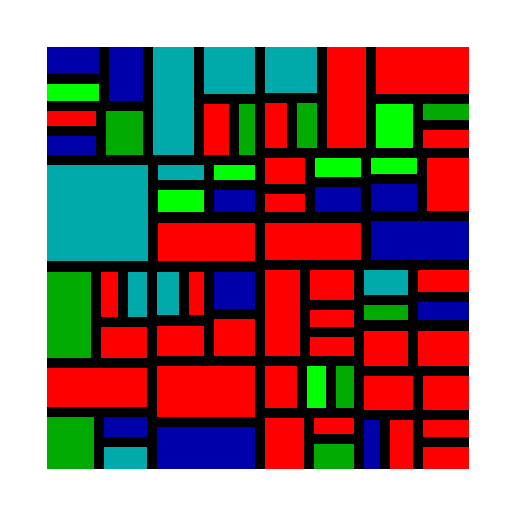

```mathematica
(*tileMap=Map[classifyEntityTile,noiseMap,{2}];
MapGrid=Map[tileToNumber,tileMap,{2}]*)
applyBlockType[#]&/@zeroBlocks;
ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

### 3d visualization

#### give heights to each block

```mathematica
getElevationNoise[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]]]
Table[AppendTo[zeroBlocks[[x]],If[MapGrid[[zeroBlocks[[x]][[1]]]][[zeroBlocks[[x]][[2]]]]==3,1,Floor[Rescale[getElevationNoise[zeroBlocks[[x]]],{0.30,0.7},{1,10}]]]],{x,zeroBlocks//Length}];
zeroBlocks
```

{{1,1,16,31,4,4,5,5,5},{1,38,32,57,4,4,4,5,5},{1,64,64,87,5,5,6,6,6},{1,94,28,123,5,5,5,6,6},{1,130,27,160,5,5,5,6,6},{1,167,60,189,3,3,4,4,4},{1,196,28,250,3,3,4,5,5},{23,1,32,31,2,2,1,1,1},{34,130,60,142,2,2,3,4,3},{34,149,60,160,4,4,5,5,5},{35,94,64,108,7,7,7,7,7},{35,115,64,123,4,4,5,5,5},{35,196,60,217,2,2,1,1,1},{35,224,43,250,4,4,4,5,5},{39,1,47,29,4,4,5,5,5},{39,36,64,57,2,2,3,4,4},{50,224,60,250,4,4,5,5,5},{54,1,64,29,3,3,4,5,4},{67,130,81,153,4,4,4,5,5},{67,160,77,186,2,2,1,1,1},{67,193,75,219,2,2,1,1,1},{67,226,97,250,3,3,3,4,4},{71,1,127,60,5,5,5,6,6},{71,67,79,93,5,5,6,6,6},{71,100,79,123,2,2,1,1,1},{82,193,97,219,2,2,3,4,4},{84,160,98,186,3,3,4,5,5},{86,67,98,93,2,2,1,1,1},{86,100,98,123,3,3,4,4,4},{88,130,98,153,5,5,5,6,6},{104,193,126,250,4,4,5,5,5},{105,67,127,123,5,5,5,6,6},{105,130,126,186,5,5,5,6,6},{133,130,183,150,5,5,5,6,6},{133,157,150,182,4,4,5,5,5},{133,189,147,214,6,6,6,7,6},{133,221,145,250,3,3,4,5,5},{134,1,184,26,4,4,5,5,5},{134,33,160,42,4,4,5,5,5},{134,49,160,59,5,5,5,6,6},{134,66,159,78,5,5,5,6,6},{134,85,159,93,6,6,7,7,7},{134,100,155,123,4,4,5,5,5},{152,221,162,250,4,4,4,5,5},{154,189,162,214,4,4,4,5,5},{157,157,166,182,3,3,4,4,4},{162,100,183,123,5,5,6,6,6},{166,66,183,93,7,7,7,8,8},{167,33,184,59,4,4,5,5,5},{169,189,189,214,3,3,4,5,5},{169,221,189,250,6,6,6,7,7},{173,157,183,182,5,5,6,6,6},{190,66,219,123,4,4,4,5,5},{190,130,214,148,5,5,5,6,6},{190,155,214,165,2,2,1,1,1},{190,172,214,182,3,3,4,4,4},{191,1,213,59,2,2,3,4,4},{196,189,215,217,5,5,6,6,6},{196,224,215,250,5,5,6,6,6},{220,1,250,28,4,4,5,5,5},{220,35,231,59,3,3,4,4,4},{221,130,250,152,7,7,7,8,7},{221,159,229,182,-1,-1,0,2,2},{222,189,250,197,1,1,2,3,3},{222,204,250,217,4,4,4,5,5},{222,224,231,250,5,5,5,6,6},{226,66,250,123,4,4,5,5,5},{236,159,250,182,1,1,2,3,3},{238,35,250,59,8,8,8,9,8},{238,224,250,250,7,7,7,7,7}}

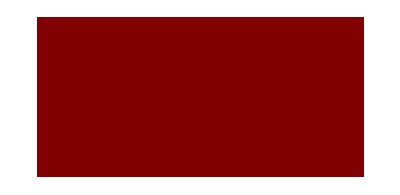

```mathematica
ArrayPlot[MapGrid2,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

blocks height(1-10)
- list of blocks
- give height to each block(add a num the end of the thingy)
roads need to be 1

### block height giver

```mathematica
ClearAll[blockHeightGiver]
blockHeightGiver[grid_,coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],h=coords[[5]]},ReplacePart[grid,{y_,a_,b_} /; (y>h&&x1<=a<=x2&&y1<=b<=y2)||(y>1&&grid[[y]][[a]][[b]]==1)->tileToNumber["background"]]]
```

```mathematica
(*COMMENT: TRY TO MAKE IT SO WE REMOVE IT BY 3D*)
```

```mathematica
MapGrid
```

```mathematica
zeroBlocks[1]
```

{{1,1,18,30,4},{1,37,14,63,4},{1,70,28,96,4},{1,103,57,125,6},{1,132,30,155,5},{1,162,30,183,2},{1,190,16,215,4},{1,222,33,250,3},{21,37,32,63,3},{23,190,33,215,4},{25,1,33,30,3},{35,70,57,96,5},{37,132,50,157,3},{37,164,66,183,5},{39,37,59,63,2},{40,1,59,30,3},{40,190,66,199,3},{40,206,66,220,5},{40,227,66,250,4},{57,132,66,157,2},{64,70,88,80,6},{64,87,88,95,3},{64,102,72,125,4},{66,1,86,35,5},{66,42,123,63,5},{73,132,93,185,3},{73,192,94,219,2},{73,226,127,250,3},{79,102,88,125,4},{93,1,108,35,4},{95,70,123,90,1},{95,97,123,105,5},{95,112,123,125,5},{100,132,127,155,6},{100,162,127,185,3},{101,192,127,201,4},{101,208,127,219,5},{115,1,123,35,4},{130,1,156,16,3},{130,23,156,33,4},{130,40,184,62,4},{130,69,155,82,4},{130,89,155,97,7},{130,104,184,125,5},{134,132,185,159,4},{134,166,185,186,5},{134,193,190,216,4},{134,223,144,250,3},{151,223,162,250,3},{162,69,184,97,7},{163,1,184,33,5},{169,223,190,250,6},{191,1,221,26,3},{191,33,221,62,2},{191,69,213,125,4},{192,132,214,186,3},{197,193,250,215,4},{197,222,219,250,5},{220,69,250,91,4},{220,98,229,125,1},{221,132,234,159,5},{221,166,250,186,0},{226,222,250,250,6},{228,1,250,62,6},{236,98,250,125,4},{241,132,250,159,9}}[1]

```mathematica
numLevels=10;
MapGrid3D=Table[MapGrid,{x,numLevels}];
Table[MapGrid3D=blockHeightGiver[MapGrid3D,zeroBlocks[[i]]],{i,zeroBlocks//Length}];
```

```mathematica
ArrayPlot3D[MapGrid3D,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],BoxRatios->{1, 1, 0.5}]
```

-Graphics3D-

### Give each block a height based on elevation noise

```mathematica
getElevationNoise[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]]]

Module[{blockType,initHeight},Table[blockType=mapGrid[[zeroBlocks[[x]][[1]]]][[zeroBlocks[[x]][[2]]]];
initHeight=Floor[Rescale[getElevationNoise[zeroBlocks[[x]]],{0.30,0.7},{1,10}]];
AppendTo[zeroBlocks[[x]],Which[blockType==tileToNumber["park"],1,blockType==tileToNumber["business"],Min[{Floor[2*initHeight],10}],blockType==tileToNumber["industrial"],Max[2,Floor[0.6*initHeight]],True,initHeight]],{x,zeroBlocks//Length}]];
```

```mathematica
blockHeightGiver[grid_,coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],h=coords//Last},ReplacePart[grid,{y_,a_,b_}/;(y>h&&x1<=a<=x2&&y1<=b<=y2)||(y>1&&grid[[y]][[a]][[b]]==1)->tileToNumber["background"]]]
```

### 3D visualization(ON HOLD)

```mathematica
numLevels=10;
mapGrid3D=Table[mapGrid,{x,numLevels}];
Table[mapGrid3D=blockHeightGiver[mapGrid3D,zeroBlocks[[i]]],{i,zeroBlocks//Length}];
```

```mathematica
ArrayPlot3D[mapGrid3D,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
{MapGrid,MapGrid2,MapGrid3,MapGrid4,MapGrid5,MapGrid6,MapGrid7,MapGrid8,MapGrid9,MapGrid10}
```

```mathematica
MapGrid//Length
```

250

```mathematica
mapGrid3D//Length
```

250

```mathematica
Counts[Flatten@MapGrid]
```

<|4→35181,1→5134,6→18448,7→3566,5→171|>

detail of blocks(adding buildings)
factor in:
- size of blocks
- noise population
-noise popularity
-elevation noise(3D)
- highrise vs lowrise(3D)
types of blocks:
- restaurants(cafe if low popularity)
- skyscrapers
- suburbs
-entertainments
-store

#### zeroblock testing

```mathematica
classifyBlock[{1, 1, 25, 44}]
land[0.55]
```

lowrise

lowrise

```mathematica
zeroBlocks={}
findDownRight[8, 2, MapGrid]
```

{}

9 2

10 2

11 2

{{8,2,10,3}}

```mathematica
|
```

```mathematica
MapGrid
```

{{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{1,1,1,1,1,1,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0}}

```mathematica
MapGrid//Grid
```

0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0

```mathematica
Position[MapGrid,0]
```

{{1,1},{1,2},{1,5},{1,6},{1,8},{1,9},{1,10},{2,1},{2,2},{2,5},{2,6},{2,8},{2,9},{2,10},{3,1},{3,2},{3,5},{3,6},{3,8},{3,9},{3,10},{4,1},{4,2},{4,5},{4,6},{4,8},{4,9},{4,10},{5,1},{5,2},{5,5},{5,6},{5,8},{5,9},{5,10},{6,1},{6,2},{6,5},{6,6},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,5},{8,6},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,5},{9,6},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,5},{10,6},{10,8},{10,9},{10,10}}

```mathematica
If[TRue,fefef]
```

```mathematica
#==1
```

```mathematica
Apply
0001
0001
0001
1111
0000

1111
1111
1111
1111
0000
```

## cool image visualization(on hold)

```mathematica
z=RandomReal[{0,255}];
octaves=6;
persistence=RandomReal[{0.3, 0.6}]
(*noiseMap=Table[Mean[Flatten[Table[octavePerlin[a, b,z,octaves,persistence ], {a, x, x+10},{b, y, y+10}]]], {x, 1,100, 10},{y,1,100, 10}]*)
noiseMap=Table[octavePerlin[x,y,1,octaves,persistence ],{x,0.1,1,0.1},{y,0.1,1,0.1}]
(*NEED TO FIGURE HOW TO MAKE THE NOISE THINGY ACC OKISH*)
```